# Contraction-path optimization

Load the paclet:

```mathematica
PacletDirectoryLoad["/path/to/TensorNetworks"];
Needs["Wolfram`TensorNetworks`"];
```

The interesting regime is dense 2D networks. The standard stress test is the PEPS overlap: a 2D lattice of tensors, copied so we have a “ket” and a “bra”, with every bond and every physical leg contracted. The result is a single scalar. The construction depends on four parameters. Each one has a specific meaning:

rows, cols: the shape of the 2D lattice. A PEPS at {rows, cols} has rows*cols sites, one tensor per site, arranged in a grid. Neighbors in the grid share a bond. Total tensors in the doubled overlap network is 2 * rows * cols.

chi: the bond dimension. Every internal bond between neighboring sites is an index of this dimension. Bigger chi means a richer ansatz and (much) more expensive contractions. This is the knob we will turn to make the contraction harder.

d: the physical dimension at each site. For a spin-1/2 system, d = 2. The physical leg of each ket tensor contracts with the physical leg of the corresponding bra tensor.

```mathematica
tn1=RandomTensorNetwork["PEPS"[{3,4},2,3]]
```

TensorNetwork[…]

```mathematica
tn1["Hypergraph"]
```

ResourceObjectupdav6dab0ddc-172b-47db-bb44-8fe0cc9737b22144133399063852469305281Local

ResourceObjectupdavbdd0a0e1-be87-4ef6-98d1-19806f60979a2144233399063852469305281Local

-Graphics-

```mathematica
tn1["FreeIndices"]
```

{18,19,20,21,22,23,24,25,26,27,28,29}

```mathematica
Developer`PackedArrayQ/@tn1["Tensors"]//Union
```

{True}

Find conventional expression using WL builtin functions (no path) using inactive trick:

```mathematica
TensorNetworkContraction[SparseTensorNetwork@tn1]
```

TensorContract[SparseArray[…]⊗SparseArray[…]⊗SparseArray[…]⊗SparseArray[…]⊗SparseArray[…]⊗SparseArray[…]⊗SparseArray[…]⊗SparseArray[…]⊗SparseArray[…]⊗SparseArray[…]⊗SparseArray[…]⊗SparseArray[…],{{1,15},{2,5},{4,19},{6,9},{8,24},{10,13},{12,29},{16,33},{17,21},{20,36},{22,26},{25,40},{27,31},{30,44},{34,37},{38,41},{42,45}}]

In above code, SparseTensorNetwork is only added for cosmetic touches.

```mathematica
exp1=TensorNetworkContraction[tn1];
finalTensorNoPath1=ActivateTensors@exp1;
finalTensorNoPath1//Dimensions
```

{3,3,3,3,3,3,3,3,3,3,3,3}

```mathematica
path1=OptimalContractionPath[tn1, Method -> "flops"]
```

{{1,2},{3,4},{5,6},{8,9},{7,8},{5,6},{1,2},{1,2},{3,4},{2,3},{1,2}}

```mathematica
finalTensorWithPath1=TensorNetworkContract[tn1,path1];
finalTensorWithPath1//Dimensions
```

{3,3,3,3,3,3,3,3,3,3,3,3}

```mathematica
Norm[Flatten[finalTensorNoPath1-finalTensorWithPath1],"Frobenius"]
```

3.79627×10^-14

Define a constructor that builds the doubled-PEPS overlap network from these four parameters:

```mathematica
ClearAll[pepsOverlapTN]
pepsOverlapTN[{rows_, cols_}, chi_, d_ : 2,args___] :=
    With[{ket = BlockRandom[SeedRandom[31 + rows * 1000 + cols * 100 + chi];
                RandomTensorNetwork["PEPS"[{rows, cols}, chi, d],args]]},
    {idx = ket["Hyperedges"]},
    {shift = Max @@ Flatten @ idx},
        TensorNetwork[
            Join[ket["Tensors"], Conjugate /@ ket["Tensors"]],
            Join[idx, MapAt[# + shift &, idx, {All, ;; -2}]]
        ]
    ]
```

```mathematica
tn2 = pepsOverlapTN[{3, 4}, 5]
```

TensorNetwork[…]

```mathematica
Length[tn2["Tensors"]]==2(3 4)
```

True

```mathematica
Length[tn2["FreeIndices"]] == 0
```

True

```mathematica
ClearAll[intermediateTrajectory,peakIntermediate]
intermediateTrajectory[expr_] := Cases[expr,
    e : IgnoringInactive[(ArrayDot | Dot | TensorContract | TensorProduct | Transpose | ArrayReshape)[__]] :>
        Wolfram`TensorNetworks`PackageScope`symbolicTensorDimensions[e],
    {0, Infinity}]

peakIntermediate[expr_] := Max[Times @@@ intermediateTrajectory[expr]]
```

```mathematica
p2=OptimalContractionPath[tn2,Method -> "flops"]
```

{{13,14},{13,14},{16,20},{18,21},{15,20},{18,19},{9,10},{1,5},{1,16},{3,15},{13,14},{5,6},{1,2},{2,11},{1,10},{8,9},{7,8},{6,7},{5,6},{2,5},{1,4},{2,3},{1,2}}

```mathematica
expr2=TensorNetworkContraction[tn2,p2];
```

```mathematica
ContractionTree[expr2]
```

-Graphics-

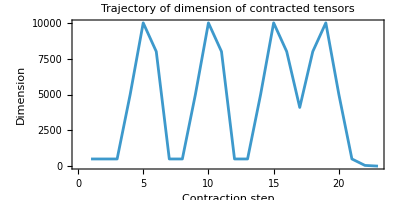

```mathematica
ListLinePlot[Times@@@intermediateTrajectory[expr2],AspectRatio->1/2,Frame->True,FrameLabel->{"Contraction step", "Dimension"},PlotLabel->"Trajectory of dimension of contracted tensors"]
```

```mathematica
peakIntermediate[TensorNetworkContraction[tn2,p2]]
```

10000

```mathematica
tn = pepsOverlapTN[{4, 5}, 5];
```

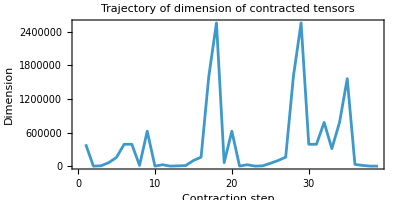

```mathematica
expr=TensorNetworkContraction[tn,OptimalContractionPath[tn]];
ListLinePlot[Times@@@intermediateTrajectory[expr],AspectRatio->1/2,Frame->True,FrameLabel->{"Contraction step", "Dimension"},PlotLabel->"Trajectory of dimension of contracted tensors"]
```

```mathematica
ClearSystemCache[];
p = OptimalContractionPath[tn, Method -> "flops"];//AbsoluteTiming
```

{39.6049,Null}

```mathematica
ClearSystemCache[];
{tOpt, rOpt} = AbsoluteTiming[TensorNetworkContract[tn, p, Method -> "ArrayDot"]];
tOpt
```

1.08723

```mathematica
ClearSystemCache[];
{tNaive, rNaive} = AbsoluteTiming[TensorNetworkContract[tn]];
tNaive
```

406.566

```mathematica
tNaive / tOpt
```

373.948

```mathematica
peakIntermediate[tn, p]
```

15625000

### Factor 1: bond dimension scales the gap

The peak intermediate grows polynomially in the bond dimension chi. For the kernel's fixed heuristic, the price of a bad intermediate also grows with chi, so the speedup from path optimization gets larger as chi increases.

Time PEPS 4x4 across three bond dimensions:

```mathematica
Table[
    With[{tn = pepsOverlapTN[{4, 4}, chi]},
        Module[{ tN, tO},
ClearSystemCache[];
tO=AbsoluteTiming[TensorNetworkContract[tn, OptimalContractionPath[tn, Method -> "flops"]]][[1]];
 ClearSystemCache[];
tN=AbsoluteTiming[TensorNetworkContract[tn]][[1]];
            <|"Bond dimension" -> chi, "Peak" -> peakIntermediate[tn, OptimalContractionPath[tn, Method -> "flops"]],
              "Time (no path)" -> tN, "Time (with path)" -> tO, "Speedup" -> tN/tO|>]
    ],{chi, {2,3,4,5, 6, 7}}]//Dataset
```

### Factor 2: lattice aspect ratio decides whether path-finding pays

Two lattices with the same total tensor count can be either chain-like or square-like. A chain has only one reasonable contraction order and the kernel finds it. A square has many; the kernel's local heuristic only sees one step at a time and gets it wrong.

```mathematica
Table[
    With[{tn = pepsOverlapTN [shape, 4]},
        Module[{p, tN, tO},
            ClearSystemCache[];
            tO =AbsoluteTiming[TensorNetworkContract[tn, OptimalContractionPath[tn, Method -> "flops"]]][[1]];
            ClearSystemCache[];
            tN= AbsoluteTiming[ TensorNetworkContract[tn]][[1]];
   Echo[shape];
            <|"Lattice Shape" -> shape, "# of Tensors" -> Length[tn["Tensors"]],
              "Peak" -> peakIntermediate[tn, OptimalContractionPath[tn, Method -> "flops"]],
              "Time (no path)" -> tN, "Time (with path)" -> tO, "Speedup" -> tN/tO|>
        ]
    ],
    {shape, {{2, 12},{3, 8}, {4, 6},{6, 4},{12,2} }}
]//Dataset
```

{2,12}

{3,8}

{4,6}

{6,4}

{12,2}